```mathematica
nonzeroRs={{{0,0},{1,0},{-1,0}}}
```

{{{0,0},{1,0},{-1,0}}}

```mathematica
ClearAll@R
```

```mathematica
Ror0[n_,k0_,k1_]:=If[MemberQ[nonzeroRs⟦n+1⟧,{k0,k1}],R[n,k0,k1],0]
R[n_,k0_,k1_,preassignop_:Simplify]:=With[{sumlim=Max@Abs@Flatten@nonzeroRs⟦;;n⟧},With[{value=(Ror0[0,0,0]-4 π^2(k0^2+k1^2))Ror0[n-1,k0,k1]+Sum[If[l0==l1==0∨(l0==k0∧l1==k1),0,(l0 k0+l1 k1)/(l0^2+l1^2)Sum[Ror0[m,l0,l1]Ror0[n-m-1,k0-l0,k1-l1],{m,0,n-1}]],{l0,-sumlim,sumlim},{l1,(*-sumlim,sumlim,*)0,0}]},If[value===0,0,
R[n,k0,k1]=preassignop@(value/n);
If[Length@nonzeroRs≤n,AppendTo[nonzeroRs,{}]];
AppendTo[nonzeroRs⟦n+1⟧,{k0,k1}];
R[n,k0,k1]]]]/;n>0
```

```mathematica
Do[Table[R[n,i,0],{i,-n-1,n+1}],{n,32}];
```

```mathematica
Grid@Table[R[1,i,j],{i,-2,2},{j,-2,2}]
```

```mathematica
Grid@Table[R[2,i,j],{i,-3,3},{j,-3,3}]
```

```mathematica
Grid@Table[R[3,i,j],{i,-4,4},{j,-4,4}]
```

```mathematica
Grid@Table[R[4,i,j],{i,-5,5},{j,-5,5}]
```

```mathematica
Grid@Table[R[5,i,j],{i,-6,6},{j,-6,6}]
```

```mathematica
Grid@Table[R[6,i,j],{i,-7,7},{j,-7,7}];
```

```mathematica
Grid@Table[R[7,i,j],{i,-8,8},{j,-8,8}];
```

```mathematica
Grid@Table[R[8,i,j],{i,-9,9},{j,-9,9}];
```

```mathematica
Grid@Table[R[9,i,j],{i,-10,10},{j,-10,10}];
```

```mathematica
Grid@Table[R[10,i,j],{i,-11,11},{j,-11,11}];
```

```mathematica
Grid@Table[R[11,i,j],{i,-12,12},{j,-12,12}];
```

```mathematica
Grid@Table[R[12,i,j],{i,-13,13},{j,-13,13}];
```

```mathematica
(*strewth*)
Table[R[i,0,i+1]==(i+1)^i/(i!)R[0,0,1]^(i+1),{i,6}]
Table[R[i,0,0]==R[0,0,0]^(i+1)/(i!),{i,6}]
```

{True,True,True,True,True,True}

{True,True,True,True,True,True}

```mathematica
Table[Distribute@(R[i,0,i]/R[0,0,1]^i),{i,6}]
```

{-4 π^2+R[0,0,0],-24 π^2+3 R[0,0,0],-102 π^2+9 R[0,0,0],-(1136 π^2)/3+80/3 R[0,0,0],-(2615 π^2)/2+625/8 R[0,0,0],-(21576 π^2)/5+1134/5 R[0,0,0]}

```mathematica
Column[Table[Coefficient[#,R[0,0,0]^3]&@Expand@Simplify[i!R[i,0,1]/R[0,0,1]-(-1)^i(2π)^(2i)+R[0,0,0](-1)^i(2π)^(2i-2)i-(-1)^i 2^(2i-5)π^(2i-4)i(i-1)R[0,0,0]^2],{i,11}],Frame->All]/.R[0,a_,b_]:>Subscript[R, a,b]
```

```mathematica
{{0}, {0}, {1}, {-16 π^2}, {160 π^4-90 Subscript[R, 0,-1] Subscript[R, 0,1]+180 Subscript[R, -1,0] Subscript[R, 1,0]}, {-1280 π^6+6880 π^2 Subscript[R, 0,-1] Subscript[R, 0,1]-11008 π^2 Subscript[R, -1,0] Subscript[R, 1,0]}, {8960 π^8-293664 π^4 Subscript[R, 0,-1] Subscript[R, 0,1]-700 Subscript[R, 0,-1]^2 Subscript[R, 0,1]^2+372288 π^4 Subscript[R, -1,0] Subscript[R, 1,0]-21000 Subscript[R, -1,0] Subscript[R, 0,-1] Subscript[R, 0,1] Subscript[R, 1,0]+22540 Subscript[R, -1,0]^2 Subscript[R, 1,0]^2}, {-57344 π^10+11521280 π^6 Subscript[R, 0,-1] Subscript[R, 0,1]+179872 π^2 Subscript[R, 0,-1]^2 Subscript[R, 0,1]^2-11063808 π^6 Subscript[R, -1,0] Subscript[R, 1,0]+22467104/5 π^2 Subscript[R, -1,0] Subscript[R, 0,-1] Subscript[R, 0,1] Subscript[R, 1,0]-22103936/5 π^2 Subscript[R, -1,0]^2 Subscript[R, 1,0]^2}, {344064 π^12-379054080 π^8 Subscript[R, 0,-1] Subscript[R, 0,1]-73140352 π^4 Subscript[R, 0,-1]^2 Subscript[R, 0,1]^2-22120 Subscript[R, 0,-1]^3 Subscript[R, 0,1]^3+271351808 π^8 Subscript[R, -1,0] Subscript[R, 1,0]-2192853376/5 π^4 Subscript[R, -1,0] Subscript[R, 0,-1] Subscript[R, 0,1] Subscript[R, 1,0]-1472468368/125 Subscript[R, -1,0] Subscript[R, 0,-1]^2 Subscript[R, 0,1]^2 Subscript[R, 1,0]+490541056 π^4 Subscript[R, -1,0]^2 Subscript[R, 1,0]^2+233572864/25 Subscript[R, -1,0]^2 Subscript[R, 0,-1] Subscript[R, 0,1] Subscript[R, 1,0]^2+368730544/125 Subscript[R, -1,0]^3 Subscript[R, 1,0]^3}, {-344064 π^14+11281240064 π^10 Subscript[R, 0,-1] Subscript[R, 0,1]+11946634240 π^6 Subscript[R, 0,-1]^2 Subscript[R, 0,1]^2+120529520 π^2 Subscript[R, 0,-1]^3 Subscript[R, 0,1]^3-5916237824 π^10 Subscript[R, -1,0] Subscript[R, 1,0]+155696546816/5 π^6 Subscript[R, -1,0] Subscript[R, 0,-1] Subscript[R, 0,1] Subscript[R, 1,0]+593471683584/125 π^2 Subscript[R, -1,0] Subscript[R, 0,-1]^2 Subscript[R, 0,1]^2 Subscript[R, 1,0]-205825785856/5 π^6 Subscript[R, -1,0]^2 Subscript[R, 1,0]^2-81273038048/25 π^2 Subscript[R, -1,0]^2 Subscript[R, 0,-1] Subscript[R, 0,1] Subscript[R, 1,0]^2-211568847488/125 π^2 Subscript[R, -1,0]^3 Subscript[R, 1,0]^3}, {10813440 π^16-315061764096 π^12 Subscript[R, 0,-1] Subscript[R, 0,1]-1348175796224 π^8 Subscript[R, 0,-1]^2 Subscript[R, 0,1]^2-73177025984 π^4 Subscript[R, 0,-1]^3 Subscript[R, 0,1]^3-447510 Subscript[R, 0,-1]^4 Subscript[R, 0,1]^4+118913564672 π^12 Subscript[R, -1,0] Subscript[R, 1,0]-9179712315392/5 π^8 Subscript[R, -1,0] Subscript[R, 0,-1] Subscript[R, 0,1] Subscript[R, 1,0]-130166251163392/125 π^4 Subscript[R, -1,0] Subscript[R, 0,-1]^2 Subscript[R, 0,1]^2 Subscript[R, 1,0]-(8030148915128 Subscript[R, -1,0] Subscript[R, 0,-1]^3 Subscript[R, 0,1]^3 Subscript[R, 1,0])/2125+14529506732032/5 π^8 Subscript[R, -1,0]^2 Subscript[R, 1,0]^2+3096484455936/5 π^4 Subscript[R, -1,0]^2 Subscript[R, 0,-1] Subscript[R, 0,1] Subscript[R, 1,0]^2-(18124351103528 Subscript[R, -1,0]^2 Subscript[R, 0,-1]^2 Subscript[R, 0,1]^2 Subscript[R, 1,0]^2)/1625+61557019924992/125 π^4 Subscript[R, -1,0]^3 Subscript[R, 1,0]^3+(23454106390096 Subscript[R, -1,0]^3 Subscript[R, 0,-1] Subscript[R, 0,1] Subscript[R, 1,0]^3)/1625+(893088624394 Subscript[R, -1,0]^4 Subscript[R, 1,0]^4)/2125}}
```

```mathematica
FindSequenceFunction@{16,160,1280,8960,344064,10813440}
```

FindSequenceFunction[{16,160,1280,8960,344064,10813440}]

```mathematica
{2^3 2,2^3 4 5,2^8 5,2^8 5 7,2^14 6 7,2^16 3 5 11}
```

{16,160,1280,8960,688128,10813440}

```mathematica
Do[Table[R[n,i,0],{i,-n-1,n+1}],{n,18}];
```

```mathematica
Table[R[n,n+1,0]==(n+1)^n/(n!)R[0,1,0]^(n+1),{n,32}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[Last@CoefficientList[R[n,n,0]/R[0,1,0]^n,R[0,0,0]]==1/2(n^(n-1)(n+1))/((n-1)!),{n,32}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[(First@CoefficientList[R[n,n,0]/R[0,1,0]^n,R[0,0,0]])/((-4 π^2 n)/((n-1)!)),{n,32}]
```

{1,3,17,142,1569,21576,355081,6805296,148869153,3660215680,99920609601,2998836525312,98139640241473,3478081490967552,132705415800984825,5423640496274200576,236389784118231290049,10944997108429625524224,536484538620663729658993,27753628754252398927872000,1511144535605115587389676001,86384329360307700891586920448,5172803056875215165371121461737,323806178222230409846783344115712,21149230300371112652462875623750625,1438808117386764390640060361003237376,101792897481143446880684083237332386721,7478214317059346764623245852370697977856,569705209621021925520432463881018697528833,44949196837031676291945674612050231296000000,3668581090206310494853015512628282761760906201,309383704859588195916522529582511623564890734592}

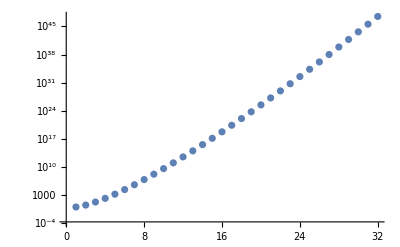

```mathematica
ListLogPlot@{1,3,17,142,1569,21576,355081,6805296,148869153,3660215680,99920609601,2998836525312,98139640241473,3478081490967552,132705415800984825,5423640496274200576,236389784118231290049,10944997108429625524224,536484538620663729658993,27753628754252398927872000,1511144535605115587389676001,86384329360307700891586920448,5172803056875215165371121461737,323806178222230409846783344115712,21149230300371112652462875623750625,1438808117386764390640060361003237376,101792897481143446880684083237332386721,7478214317059346764623245852370697977856,569705209621021925520432463881018697528833,44949196837031676291945674612050231296000000,3668581090206310494853015512628282761760906201,309383704859588195916522529582511623564890734592}
```